## Hamiltonians

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with free bc *)
ω=N [(Sqrt[5]-1)/2];
rot=28; (* rotate the sequence of couplings *)
fib[n_]:=IntegerPart[ω( n+1+rot)]-IntegerPart[ω (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];

hf[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with periodic bc *)
hpn[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
AppendTo[tbl,{1,F2}->tw];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Harper *)
hharp[p_,q_,ϕ_,λ_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*periodic boundary conditions*)AppendTo[hopping,{1,q}->-1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.λ Cos[2 π p i/q+ϕ],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfib[n_,ϕ_,λ_]:=hharp[Fibonacci[n-1],Fibonacci[n],ϕ,λ];
SetAttributes[hfib,Listable];
```

## Cookie-cutter map

```mathematica
(* system size is fib(i+2) *)
n=16;
(* jump amplitude ratio *)
ts=1.;
ρ=.5;
tw=ρ ts;
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[n,tw,ts]]];
vpa=Sort[Eigenvalues[ha[n,tw,ts]]];
(* spectres des systèmes de taille i-2 p et anti-p *)
vpp2=Sort[Eigenvalues[hp[n-2,tw,ts]]];
vpa2=Sort[Eigenvalues[ha[n-2,tw,ts]]];
(* spectres des systèmes de taille i-3 p et anti-p *)
vpp3=Sort[Eigenvalues[hp[n-3,tw,ts]]];
vpa3=Sort[Eigenvalues[ha[n-3,tw,ts]]];

(* bandlists *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
```

MapThread::mptd: Object vpaN at position {2, 1} in MapThread[Abs[#1 - #2] &, {vpaN, vppN}] has only 0 of required 1 dimensions.

```mathematica
glue[{l1_,l2_}]:=MapThread[{#1,#2}&,{l1,l2}];
FiboCookie[e_,e2_,e3_]:=Block[{maps,eleft=e[[1;;Length[e2]]],emid=e[[Length[e2]+1;;Length[e2]+Length [e3]]],eright=e[[Length[e2]+Length[e3]+1;;]]},
maps=glue/@{{eleft,e2},{emid,Reverse@e3},{eright,e2}};
maps]
```

```mathematica
cookie05=FiboCookie[vpp,vpp2,vpp3];
```

```mathematica
cookie[n_,ρ_]:=Block[{ts=1.,tw=ρ,vpp,vpp2,vpp3},
vpp=Sort[Eigenvalues[hp[n,tw,ts]]];
vpp2=Sort[Eigenvalues[hp[n-2,tw,ts]]];
vpp3=Sort[Eigenvalues[hp[n-3,tw,ts]]];
FiboCookie[vpp,vpp2,vpp3]]
```

```mathematica
cookie1=cookie[16,1.];
cookie09=cookie[16,0.9];
cookie05=cookie[16,0.5];
```

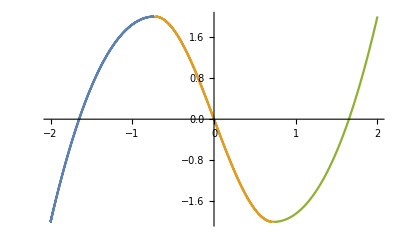

```mathematica
p0=ListPlot[cookie1,Joined->True]
```

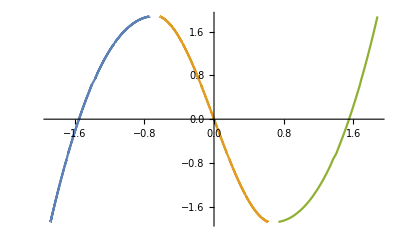

```mathematica
p09=ListPlot[cookie09,Joined->True]
```

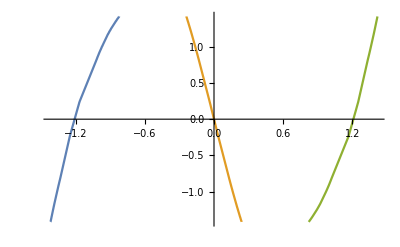

```mathematica
p05=ListPlot[cookie05,Joined->True]
```

```mathematica
fcookie05=Transpose@Flatten[cookie05,1];
```

```mathematica
fcookie09=Transpose@Flatten[cookie09,1];
```

```mathematica
Manipulate[Show[p0,ListPlot[MapThread[{s1#1,s2#2}&,fcookie09],Joined->True]],{s1,1,2},{s2,1,2}]
```

```mathematica
Manipulate[Show[p0,ListPlot[MapThread[{s1#1,s2#2}&,fcookie05],Joined->True]],{s1,1,2},{s2,0.01,2}]
```

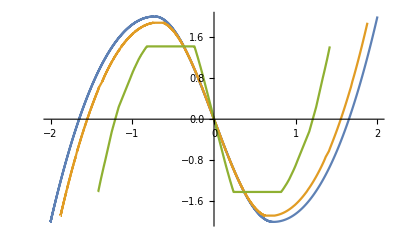

```mathematica
ListPlot[Flatten[#,1]&/@{cookie1,cookie09,cookie05},Joined->True]
```